```mathematica
FactInteger[n_]:=If[n==1,{},FactorInteger[n]]
d[n_,z_]:=Product[1/(p[[2]]!) Pochhammer[z,p[[2]]],{p,FactInteger[n]}]
```

```mathematica
pk[n_,0]:=pk[n,0]=If[n==1,1,0]
pk[n_,1]:=pk[n,1]=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
pk[n_,k_]:=pk[n,k]=Sum[pk[j,k-1]pk[n/j,1],{j,Divisors[n]}]
dv2[n_,k_]:=Sum[k^j/(j!) pk[n,j],{j,0,N[Log[n]/Log[2]]}]
dv3[n_,k_] := dv3[n,k]=pk[n,0]+k pk[n,1] + k^2/2 pk[n,2] + k^3/6 pk[n,3] + k^4/24 pk[n,4] + k^5 / 120 pk[n,5] + k^6/720 pk[n,6] + k^7/(7!) pk[n,7] + k^8/(8!) pk[n,8]
cosp[n_,k_] := cosp[n,k]= pk[n,0]- k^2/2 pk[n,2] + k^4/24 pk[n,4] - k^6/720 pk[n,6] + k^8/(8!) pk[n,8]
sinp[n_,k_] := sinp[n,k]=k pk[n,1] - k^3/6 pk[n,3] + k^5 / 120 pk[n,5] -  k^7/(7!) pk[n,7]
```

```mathematica
Table[{n,a=dv3[n,I], b=(cosp[n,1]+I sinp[n,1]),a-b},{n,1,100}] // TableForm
```

1 | 1 | 1 | 0
2 | ⅈ | ⅈ | 0
3 | ⅈ | ⅈ | 0
4 | -1/2+ⅈ/2 | -1/2+ⅈ/2 | 0
5 | ⅈ | ⅈ | 0
6 | -1 | -1 | 0
7 | ⅈ | ⅈ | 0
8 | -1/2+ⅈ/6 | -1/2+ⅈ/6 | 0
9 | -1/2+ⅈ/2 | -1/2+ⅈ/2 | 0
10 | -1 | -1 | 0
11 | ⅈ | ⅈ | 0
12 | -1/2-ⅈ/2 | -1/2-ⅈ/2 | 0
13 | ⅈ | ⅈ | 0
14 | -1 | -1 | 0
15 | -1 | -1 | 0
16 | -5/12 | -5/12 | 0
17 | ⅈ | ⅈ | 0
18 | -1/2-ⅈ/2 | -1/2-ⅈ/2 | 0
19 | ⅈ | ⅈ | 0
20 | -1/2-ⅈ/2 | -1/2-ⅈ/2 | 0
21 | -1 | -1 | 0
22 | -1 | -1 | 0
23 | ⅈ | ⅈ | 0
24 | -1/6-ⅈ/2 | -1/6-ⅈ/2 | 0
25 | -1/2+ⅈ/2 | -1/2+ⅈ/2 | 0
26 | -1 | -1 | 0
27 | -1/2+ⅈ/6 | -1/2+ⅈ/6 | 0
28 | -1/2-ⅈ/2 | -1/2-ⅈ/2 | 0
29 | ⅈ | ⅈ | 0
30 | -ⅈ | -ⅈ | 0
31 | ⅈ | ⅈ | 0
32 | -1/3-ⅈ/12 | -1/3-ⅈ/12 | 0
33 | -1 | -1 | 0
34 | -1 | -1 | 0
35 | -1 | -1 | 0
36 | -ⅈ/2 | -ⅈ/2 | 0
37 | ⅈ | ⅈ | 0
38 | -1 | -1 | 0
39 | -1 | -1 | 0
40 | -1/6-ⅈ/2 | -1/6-ⅈ/2 | 0
41 | ⅈ | ⅈ | 0
42 | -ⅈ | -ⅈ | 0
43 | ⅈ | ⅈ | 0
44 | -1/2-ⅈ/2 | -1/2-ⅈ/2 | 0
45 | -1/2-ⅈ/2 | -1/2-ⅈ/2 | 0
46 | -1 | -1 | 0
47 | ⅈ | ⅈ | 0
48 | -(5 ⅈ)/12 | -(5 ⅈ)/12 | 0
49 | -1/2+ⅈ/2 | -1/2+ⅈ/2 | 0
50 | -1/2-ⅈ/2 | -1/2-ⅈ/2 | 0
51 | -1 | -1 | 0
52 | -1/2-ⅈ/2 | -1/2-ⅈ/2 | 0
53 | ⅈ | ⅈ | 0
54 | -1/6-ⅈ/2 | -1/6-ⅈ/2 | 0
55 | -1 | -1 | 0
56 | -1/6-ⅈ/2 | -1/6-ⅈ/2 | 0
57 | -1 | -1 | 0
58 | -1 | -1 | 0
59 | ⅈ | ⅈ | 0
60 | 1/2-ⅈ/2 | 1/2-ⅈ/2 | 0
61 | ⅈ | ⅈ | 0
62 | -1 | -1 | 0
63 | -1/2-ⅈ/2 | -1/2-ⅈ/2 | 0
64 | -19/72-ⅈ/8 | -19/72-ⅈ/8 | 0
65 | -1 | -1 | 0
66 | -ⅈ | -ⅈ | 0
67 | ⅈ | ⅈ | 0
68 | -1/2-ⅈ/2 | -1/2-ⅈ/2 | 0
69 | -1 | -1 | 0
70 | -ⅈ | -ⅈ | 0
71 | ⅈ | ⅈ | 0
72 | 1/6-ⅈ/3 | 1/6-ⅈ/3 | 0
73 | ⅈ | ⅈ | 0
74 | -1 | -1 | 0
75 | -1/2-ⅈ/2 | -1/2-ⅈ/2 | 0
76 | -1/2-ⅈ/2 | -1/2-ⅈ/2 | 0
77 | -1 | -1 | 0
78 | -ⅈ | -ⅈ | 0
79 | ⅈ | ⅈ | 0
80 | -(5 ⅈ)/12 | -(5 ⅈ)/12 | 0
81 | -5/12 | -5/12 | 0
82 | -1 | -1 | 0
83 | ⅈ | ⅈ | 0
84 | 1/2-ⅈ/2 | 1/2-ⅈ/2 | 0
85 | -1 | -1 | 0
86 | -1 | -1 | 0
87 | -1 | -1 | 0
88 | -1/6-ⅈ/2 | -1/6-ⅈ/2 | 0
89 | ⅈ | ⅈ | 0
90 | 1/2-ⅈ/2 | 1/2-ⅈ/2 | 0
91 | -1 | -1 | 0
92 | -1/2-ⅈ/2 | -1/2-ⅈ/2 | 0
93 | -1 | -1 | 0
94 | -1 | -1 | 0
95 | -1 | -1 | 0
96 | 1/12-ⅈ/3 | 1/12-ⅈ/3 | 0
97 | ⅈ | ⅈ | 0
98 | -1/2-ⅈ/2 | -1/2-ⅈ/2 | 0
99 | -1/2-ⅈ/2 | -1/2-ⅈ/2 | 0
100 | -ⅈ/2 | -ⅈ/2 | 0

```mathematica
FF[n_] :=Sin[n]^2+Cos[n]^2
```

```mathematica
N[FF[8]]
```

1.

```mathematica
sinp[8,3]
```

-7/2

```mathematica
sinp[9,2]+cosp[9,2]
```

-1

```mathematica
Sinp[n_,k_] := Sum[ sinp[j,k],{j,1,n}]
```

```mathematica
Sinp[100,2]
```

-199/2

```mathematica
Cosp[n_,k_] := Sum[ cosp[j,k],{j,1,n}]
```

```mathematica
Cosp[100,2]
```

-2029/18

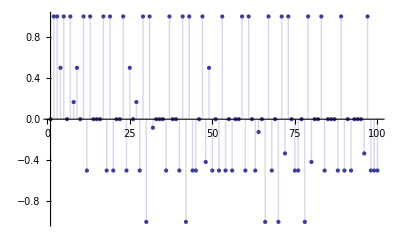

```mathematica
DiscretePlot[sinp[n,1],{n,1,100}]
```

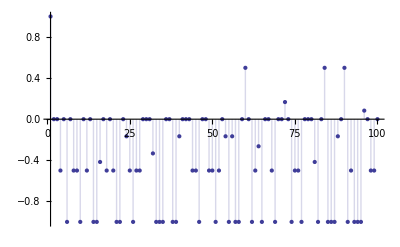

```mathematica
DiscretePlot[cosp[n,1],{n,1,100}]
```

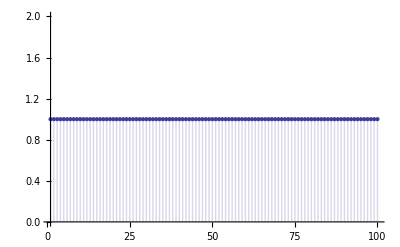

```mathematica
DiscretePlot[dv3[n,1],{n,1,100}]
```

```mathematica
Table[{n,a=cosp[n,1], b=(sinp[n,1])},{n,1,100}] // TableForm
```

1 | 1 | 0
2 | 0 | 1
3 | 0 | 1
4 | -1/2 | 1/2
5 | 0 | 1
6 | -1 | 0
7 | 0 | 1
8 | -1/2 | 1/6
9 | -1/2 | 1/2
10 | -1 | 0
11 | 0 | 1
12 | -1/2 | -1/2
13 | 0 | 1
14 | -1 | 0
15 | -1 | 0
16 | -5/12 | 0
17 | 0 | 1
18 | -1/2 | -1/2
19 | 0 | 1
20 | -1/2 | -1/2
21 | -1 | 0
22 | -1 | 0
23 | 0 | 1
24 | -1/6 | -1/2
25 | -1/2 | 1/2
26 | -1 | 0
27 | -1/2 | 1/6
28 | -1/2 | -1/2
29 | 0 | 1
30 | 0 | -1
31 | 0 | 1
32 | -1/3 | -1/12
33 | -1 | 0
34 | -1 | 0
35 | -1 | 0
36 | 0 | -1/2
37 | 0 | 1
38 | -1 | 0
39 | -1 | 0
40 | -1/6 | -1/2
41 | 0 | 1
42 | 0 | -1
43 | 0 | 1
44 | -1/2 | -1/2
45 | -1/2 | -1/2
46 | -1 | 0
47 | 0 | 1
48 | 0 | -5/12
49 | -1/2 | 1/2
50 | -1/2 | -1/2
51 | -1 | 0
52 | -1/2 | -1/2
53 | 0 | 1
54 | -1/6 | -1/2
55 | -1 | 0
56 | -1/6 | -1/2
57 | -1 | 0
58 | -1 | 0
59 | 0 | 1
60 | 1/2 | -1/2
61 | 0 | 1
62 | -1 | 0
63 | -1/2 | -1/2
64 | -19/72 | -1/8
65 | -1 | 0
66 | 0 | -1
67 | 0 | 1
68 | -1/2 | -1/2
69 | -1 | 0
70 | 0 | -1
71 | 0 | 1
72 | 1/6 | -1/3
73 | 0 | 1
74 | -1 | 0
75 | -1/2 | -1/2
76 | -1/2 | -1/2
77 | -1 | 0
78 | 0 | -1
79 | 0 | 1
80 | 0 | -5/12
81 | -5/12 | 0
82 | -1 | 0
83 | 0 | 1
84 | 1/2 | -1/2
85 | -1 | 0
86 | -1 | 0
87 | -1 | 0
88 | -1/6 | -1/2
89 | 0 | 1
90 | 1/2 | -1/2
91 | -1 | 0
92 | -1/2 | -1/2
93 | -1 | 0
94 | -1 | 0
95 | -1 | 0
96 | 1/12 | -1/3
97 | 0 | 1
98 | -1/2 | -1/2
99 | -1/2 | -1/2
100 | 0 | -1/2

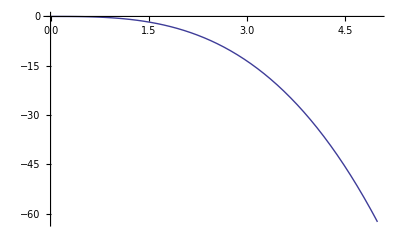

```mathematica
Plot[ N[sinp[24,x]],{x,0,5}]
```

```mathematica
PP[n_,k_, a_] := PP[n,k, a]=Sum[ d[j,a] / k - PP[Floor[n/j],k+1,a],{j,2,n}]
PS[n_,k_, a_] := PS[n,k, a]=Sum[ d[j,a](1 / k - PS[Floor[n/j],k+1,a]),{j,2,n}]
```

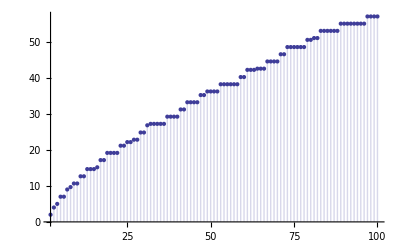

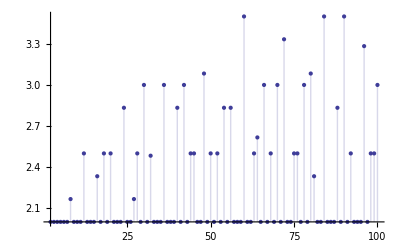

```mathematica
DiscretePlot[ PS[n,1,2],{n,2,100}]
```

```mathematica
PP[n_,k_, a_] := PP[n,k, a]=Sum[ d[j,a] / k - PP[Floor[n/j],k+1,a],{j,2,n}]
PS[n_,k_, a_] := PS[n,k, a]=Sum[ d[j,a](1 / k - PS[Floor[n/j],k+1,a]),{j,2,n}]
PS[100,2,.0000000001]/.0000000001 * 2
```

28.5333

```mathematica
PS[100,3,.0000000001]/.0000000001 * 3
```

28.5333

```mathematica
N[PS[100,3,1]* 3]
```

8.38214

```mathematica
DD[n_,k_]:=Sum[d[j,k],{j,1,n}]
Sum[ d[j,3],{j,2,100}]
```

1470

```mathematica
DD[100,3] - DD[100,0]
```

1470

```mathematica
(x^3-1)
```

-1+x^3

```mathematica
Expand[(x^3-1)^2]
```

1-2 x^3+x^6

```mathematica
Sum[ d[j,3*.2]d[k,3*.2],{j,2,100},{k,2,100/j}]
```

67.767

```mathematica
DD[100,6*.2] - 2 DD[100,3*.2] + DD[100,0*.2]
```

67.767

```mathematica
Sum[ d[j,2]d[k,2],{j,2,100},{k,2,100/j}]
```

2612

```mathematica
DD[100,4] - 2 DD[100,2] + DD[100,0]
```

2612

```mathematica
Expand[(x^2-1)^4]
```

1-4 x^2+6 x^4-4 x^6+x^8

```mathematica
Sum[ d[j,2]d[k,2] d[m,2]d[l,2],{j,2,1000},{k,2,1000/j},{l,2,1000/(j k)},{m,2,1000/(j k l)}]
```

695709

```mathematica
DD[1000,8] - 4 DD[1000,6] + 6 DD[1000,4] - 4 DD[1000,2] + DD[1000,0]
```

695709

```mathematica
DDD[ n_, k_, a_ ] := Sum[(-1)^(k-j) Binomial[k,j] DD[n,a j],{j,0,k}]
```

```mathematica
DDD[1000,9,2]
```

5120

```mathematica
FactInteger[n_]:=If[n==1,{},FactorInteger[n]]
d[n_,z_]:=Product[1/(p[[2]]!) Pochhammer[z,p[[2]]],{p,FactInteger[n]}]
DD[n_,k_]:=Sum[d[j,k],{j,1,n}]
PrimeCount[n_, a_ ] := Sum[ (-1)^(k+1)/k Sum[(-1)^(k-j) Binomial[k,j] DD[n,a j],{j,0,k}],{k,1,N[Log[n]/Log[2]]}]
```

```mathematica
N[PPP[100,I]/I]
```

28.5333

```mathematica
Sum[ (-1)^(k+1)/k (x^a-1)^k,{k,1,Infinity}]
```

```mathematica
Log[x^a]==a Log[x]
```

Log[x^a]==a Log[x]

```mathematica
Integrate[ d[2,-t],{t,1,2}]
```

-3/2

```mathematica
d[3,3]
```

3

```mathematica
N[PrimeCount[100,ZetaZero[1]]]
```

14.2667+403.311 ⅈ

```mathematica
Kappa[n_] := FullSimplify[ MangoldtLambda[ n]/Log[n]]
PB[n_, k_] := Sum[ BernoulliB[k]/(k!) + Kappa[ j]PB[Floor[n/j],k+1],{j,2,n}]
PB[100,0]
```

428/15

```mathematica
Kappa[n_] := FullSimplify[ MangoldtLambda[ n]/Log[n]]
PB[n_, k_,a_] := Sum[ BernoulliB[k]/(k!) + Kappa[j]PB[Floor[n/j],k+1,a],{j,2,n}]
PB[100,0,1]
```

428/15